{{300,1},{760,1.7},{1900,5},{2500,9},{3200,14},{3805,19}}

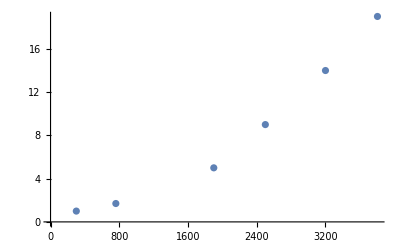

```mathematica
tutild={{300,1},{760,1.7},{1900,5},{2500,9},{3200,14},{3805,19}}
```

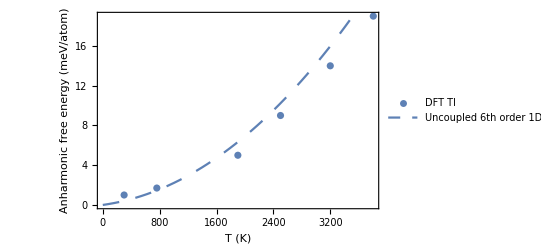

```mathematica
f[x_]:=0.001x+0.0000012x^2+0.000000000015x^3
EinsteinTIplot=Show[{ListPlot[tutild,Frame->True,FrameLabel->{"T (K)","Anharmonic free energy (meV/atom)"},PlotLegends->Placed[{"DFT TI"},{0.13,0.8}]],Plot[f[x],{x,0,3800},PlotStyle->Dashing[0.03],PlotLegends->Placed[{"Uncoupled 6th order 1D Einstein"},{0.4,0.9}]]}]
```

```mathematica
Export["/Users/tom/scripts/XMat-slides/13-Dec-17-CMTH/images/EinsteinTIplot.png",EinsteinTIplot]
```

/Users/tom/scripts/XMat-slides/13-Dec-17-CMTH/images/EinsteinTIplot.png